```mathematica
NotebookDirectory[]
```

/Users/maxfrankel/Desktop/Jun Ye/Daily Files/20241224/

#### ABCD matrix evolution inside a confocal cavity

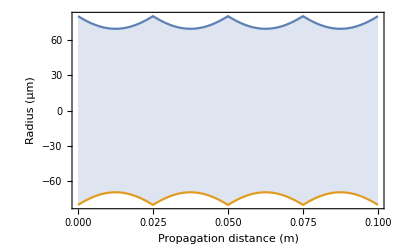

```mathematica
ABCD[z_]:= Which[
z<L,({{1, z}, {0, 1}}),
z==L,({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
L<z<2L,({{1, z-L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
z==2L,({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
2L<z<3L,({{1, z-2L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
z==3L,({{1, 0}, {-2/Rlens, 1}}). ({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
3L<z<4L,({{1, z-3L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}). ({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}),
z==4L,({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}). ({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}})
];

(* incident beam parameters *)
wi =0.00008008615870885669; (* initial waist in m *)
λ = 698*10^-9; (* wavelength in m*)
Ri =-0.05; (* initial wavefront radius in m *)

(* cavity parameters *)
Rlens=50*10^-3; (* lens curvature in m *)
L=25*10^-3 ; (* cavity length in m *)

(* evolution of waist and radius of curvature inside cavity *)
qi = 1/(1/Ri-I λ/(π wi^2));
qf[z_] := (qi*ABCD[z][[1,1]]+ABCD[z][[1,2]])/(qi*ABCD[z][[2,1]]+ABCD[z][[2,2]])
w[z_]:= √(λ/(-π Im[1/qf[z]]))//N
R[z_] := 1/(N[Re[1/qf[z]]])
plt=Plot[{w[z]*10^6,-w[z]*10^6},{z,0,4L},Filling->{1->{2}},Frame->True,FrameLabel->{"Propagation distance (m)","Radius (μm)"}]
```

```mathematica
w02[z_]:=w[z]/Sqrt[1+((π w[z]^2/λ)/R[z])^2] (* waist size *)
```

```mathematica
Manipulate[N[w02[z]],{z,0,4L}] (* smallest waist within section of cavity *)
Manipulate[w[z],{z,0,4L}] (* beam radius *)
Manipulate[R[z],{z,0,4L}] (* wavefront radius *)
```

#### Calculation of stable cavity mode

```mathematica
(* round-trip ABCD matrix *)
ABCDrt=({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}). ({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-2/Rlens, 1}}).({{1, L}, {0, 1}});
ABCDrt//MatrixForm
```

(-1 | -1/40
40 | 0)

```mathematica
(* find solution q that remains unchanged under round-trip *)
qsols=NSolve[q==(ABCDrt[[1,1]]*q + ABCDrt[[1,2]])/(ABCDrt[[2,1]]*q+ABCDrt[[2,2]]),q]
```

{{q→-0.0125-0.0216506 ⅈ},{q→-0.0125+0.0216506 ⅈ}}

```mathematica
wq[q_]:= √(λ/(-π Im[1/q]))//N
Rq[q_] := 1/(N[Re[1/q]])
```

```mathematica
wq[q/.qsols[[1]]] (* not feasible, imaginary waist *)
Rq[q/.qsols[[1]]]
wq[q/.qsols[[2]]]
Rq[q/.qsols[[2]]]
```

0.+0.0000800862 ⅈ

-0.05

0.0000800862

-0.05